## Prep

### Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

### Values

```mathematica
wmhz=π*2.*^6;
wkhz=π*2.*^3;
ns=1.*^-9;
```

```mathematica
ωd=82.*wmhz;
ωsec=751.5*wkhz;
```

## Params

```mathematica
xArr=Range[0.,2000.,0.5]*ns;
```

```mathematica
Vr0=0.4;ϕr0=0.;
Vb0=0.8;ϕb0=0.2;
Vd0=0.1;ϕd0=0.;
```

```mathematica
Vr1=0.0;ϕr1=0.0;
Vb1=0.0;ϕb1=0.0;
(*Vd1=0.3;ϕd1=0.25;*)
Vd1=0.;ϕd1=0.;
```

## Calc

```mathematica
(*ch0*)
dataY0=(Vr0*Cos[(ωd-ωsec)*#+(ϕr0*2.π)]
+Vb0*Cos[(ωd+ωsec)*#+(ϕb0*2.π)]
+Vd0*Cos[ωd*#+(ϕd0*2.π)])&/@xArr;
dataArr0=Transpose[{xArr/ns,dataY0}];
```

```mathematica
(*ch1*)
dataY1=(Vr1*Cos[(ωd-ωsec)*#+(ϕr1*2.π)]
+Vb1*Cos[(ωd+ωsec)*#+(ϕb1*2.π)]
+Vd1*Cos[ωd*#+(ϕd1*2.π)])&/@xArr;
dataArr1=Transpose[{xArr/ns,dataY1}];
```

```mathematica
(*leakage*)
dataArr2=Transpose[{xArr/ns,dataY0+1.0*dataY1}];
```

### Plot

```mathematica
(*title*)
figTitle0="CH0:\t V_r/V_b = "<>ToString[Vr0]<>"V/"<>ToString[Vb0]<>"V \t ϕ_r/ϕ_b = "<>ToString[ϕr0]<>"/"<>ToString[ϕb0];
figTitle1="CH1:\t V_r/V_b = "<>ToString[Vr1]<>"V/"<>ToString[Vb1]<>"V \t ϕ_r/ϕ_b = "<>ToString[ϕr1]<>"/"<>ToString[ϕb1];
figTitle=figTitle0<>"\n"<>figTitle1;
```

```mathematica
(*plot*)
figPlot=ListLinePlot[
{(*dataArr0,dataArr1,*)dataArr2},
PlotRange->{Full,Full},
PlotLegends->{"CH0","CH1"},
FrameLabel->{ 
{Style["Voltage (V)",{Black,Directive[15]}],None},
{Style["Time (ns)",{Black,Directive[15]}],
Style[figTitle,{Black,Directive[15]}]}
}
];
```

## Show

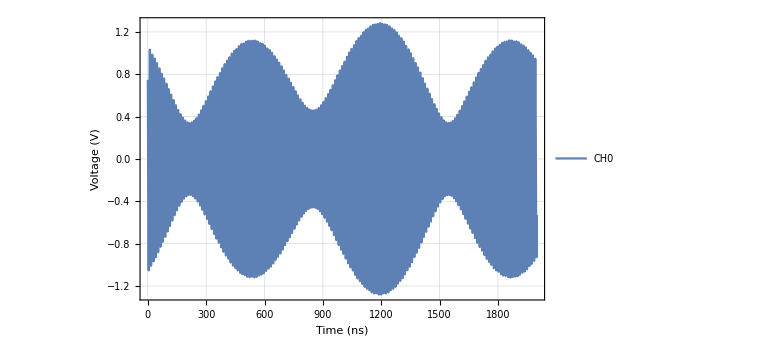

```mathematica
figPlot
```